# VALIDAÇÃO DE UM SISTEMA DE CABOS PLANO DE 10Km

## Aluno: Pulo Eduardo Darski Rocha Prof.: Dr. Antonio Carlos Siqueira de Lima

## Dados Iniciais do programa

```mathematica
Off[General::"spell",General::"spell1"];
```

```mathematica
plstyle1={AbsoluteThickness[2],RGBColor[1,0,0]};
plstyle3={AbsoluteThickness[2],RGBColor[0,0,1],Dashing[{.02}]};
plstyle2={AbsoluteThickness[2],RGBColor[0,1,0]};
```

## Dados de Entrada

Dimensões dos cabos

```mathematica
r1=2.00 10^-2;
r2=3.30 10^-2;
r3=3.75 10^-2;
r4=3.90 10^-2;
r5=4.40 10^-2;
r6=4.80 10^-2;
```

Constantes Elétricas e Parâmetros do Solo por metro

```mathematica
μ=4.0 π 10^-7;
ϵ=8.854*10^-12;
ϵcs=2.6;
ϵsa=3.0;
ϵag=3.0;
ϵ1=ϵcs ϵ;
ϵ2=ϵsa ϵ;
ϵ3=ϵag ϵ;
ρa=0.171 10^-6;
ρs=0.2065 10^-6;
ρc=1.70 10^-8;
μc=1;
μs=1;
μa=80;
ρ=100;
```

## Configuração da Rede

Espaçamento dos condutores

```mathematica
x1=0;x3=r6;x5=2r6;
h1=1.0;h3=1.0-Sqrt[(2 r6)^2-r6^2];h5=1.0;
xc={x1,x1,x1,x3,x3,x3,x5,x5,x5};
hc={h1,h1,h1,h3,h3,h3,h5,h5,h5};
r={r1,r3,r6,r1,r3,r6,r1,r3,r6};
```

```mathematica
mostra=Table[{Circle[{xc[[i]],-hc[[i]]},r[[i]]]},{i,1,9}];
```

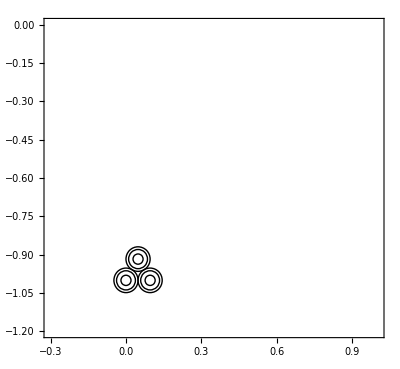

-Graphics-

```mathematica
Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->True,PlotRange->{{-0.3,1},{-1.2,-0.0}}]
```

S_ij é a distância entre o cabo  i e  j, d é a soma  das profundidades do cabo i para  o cabo j

```mathematica
s13=.35;
s35=s13;
s15=2*s13;
```

Espaçamento dos condutores

```mathematica
de=√(r6^2+(2hc[[1]])^2);
d13=√((x1-x3)^2+(hc[[1]]-hc[[4]])^2);
dc13=√((x1-x3)^2+(hc[[1]]+hc[[4]])^2);
d15=√((x1-x5)^2+(hc[[1]]-hc[[7]])^2);
dc15=√((x1-x5)^2+(hc[[1]]+hc[[7]])^2);
```

## Frequência de Interesse

#### Faixa de Frequência

```mathematica
logspace[f1_,f2_,n_]:=Table[10^(f1+((f2-f1)/(n-1))*x),{x,0,n-1}]//N;
f=logspace[-2,6,120];
nf=Dimensions[f][[1]];
```

#### Listas

```mathematica
S=Table[0,{n,1,nf}];
S1=Table[0,{n,1,nf}];

Tran=Table[0,{n,1,nf}];
λ=Table[0,{n,1,nf}];
Γ=Table[0,{n,1,nf}];
λm=Table[0,{n,1,nf}];

Tran1=Table[0,{n,1,nf}];
λ1=Table[0,{n,1,nf}];
Γ1=Table[0,{n,1,nf}];
λm1=Table[0,{n,1,nf}];

Zss=Table[0,{n,1,nf}];
Zcs=Table[0,{n,1,nf}];
```

## Parametros

```mathematica
Timing[Do[{ω=2 π f[[nm]],
s=I ω,

(*--------------------------Matriz de Admitancia Shunt---------------------------*)

y1=ⅉ ω 2 π ϵ1/Log[r2/r1],
y2=ⅉ ω 2 π ϵ2/Log[r4/r3],
y3=ⅉ ω 2 π ϵ2/Log[r6/r5],
Ycond={{y1, -y1,0},{-y1, y1+y2,-y2},{0, -y2,y2+y3}},
Zero=Table[0,{i,1,3},{j,1,3}],
Ycabo=ArrayFlatten[{{Ycond,Zero,Zero},{Zero,Ycond,Zero},{Zero,Zero,Ycond}}],


(*--------------------------Matriz de Impedância Série---------------------------*)

ηc=√((ⅉ  ω μ)/ρc),
ηs=√((ⅉ  ω μ)/ρs),
ηa=√((ⅉ  ω μ)/ρa),
ηg=√((ⅉ  ω μ)/ρ),
z11=(ρc ηc)/(2π r1)BesselI[0,ηc r1]/BesselI[1,ηc r1],
z12=(I ω μ)/(2π)Log[r2/r1],
Den=BesselI[1,ηs r3]BesselK[1,ηs r2]-BesselI[1,ηs  r2]BesselK[1,ηs r3],
z2i=(ρs ηs)/(2π r2)1/Den(BesselI[0,ηs r2]BesselK[1, ηs r3]+BesselK[0,ηs  r2]BesselI[1,ηs  r3]),
z2o=(ρs ηs)/(2π r3)1/Den(BesselI[0,ηs r3]BesselK[1, ηs r2]+BesselK[0,ηs r3]BesselI[1,ηs r2]),
z2m=ρs/(2π r2 r3)1/Den,
z23=(I ω μ)/(2π)Log[r4/r3],
Den2=BesselI[1,ηa r5]BesselK[1,ηa r4]-BesselI[1,ηa  r4]BesselK[1,ηa r5],
z3i=(ρa ηa)/(2π r4)1/Den2(BesselI[0,ηa r4]BesselK[1, ηa r5]+BesselK[0,ηa  r4]BesselI[1,ηa  r5]),
z3o=(ρa ηa)/(2π r5)1/Den2(BesselI[0,ηa r5]BesselK[1, ηa r4]+BesselK[0,ηa r5]BesselI[1,ηa r4]),
z3m=ρa/(2π r4 r5)1/Den2,
z34=ⅉ(I ω μ)/(2π)Log[r6/r5],

zcc=z11+z12+z2i+z2o-2 z2m+z23+z3i+z3o-2 z3m+z34,
zss=z2o+z23+z3i+z3o-2 z3m+z34,
zaa=z3o+z34,
zcs=z2o-z2m+z23+z3i+z3o-2 z3m+z34,
zca=z3o+z34-z3m,
zsa=zca,

zint={{zcc,zcs,zca},{zcs,zss,zsa},{zca,zsa,zaa}},
zero=Table[0,{i,1,3},{j,1,3}],
Zi=ArrayFlatten[{{zint,zero,zero},{zero,zint,zero},{zero,zero,zint}}],

(*----Efeito de proximidade----*)

lim=15,
funprox=∑_(y=1)^lim (I ω μ r5^(y-1))/π(r5/d15)^y (1/d15)^y BesselI[y,ηa r5]/(y/r5 BesselI[y,ηa r5]+ηa/μa BesselI[y-1,ηa r5]),

zproxii=Table[2 funprox,{i,1,3},{j,1,3}],
zproxij=Table[funprox,{i,1,3},{j,1,3}],

Zpe=ArrayFlatten[{{zproxii,zproxij,zproxij},{zproxij,zproxii,zproxij},{zproxij,zproxij,zproxii}}],


(*----Impedancia de retorno----*)

zgprop=Table[(ⅈ ω μ)/(2π)(BesselK[0,r6 ηg]+((de^2)  BesselK[2,ηg  de])/de^2-2 (de^2) Exp[-2hc[[1]] ηg]/(ηg^2 ( de^4))( 1+2hc[[1]] ηg )),{i,1,3},{j,1,3}],zsolo1=Table[(ⅈ ω μ)/(2π)(BesselK[0,d13 ηg]+((dc13^2)  BesselK[2,ηg  dc13])/dc13^2-2((dc13)^2) Exp[-2hc[[1]] ηg]/((ηg^2) (dc13)^4)( 1+2hc[[1]] ηg )),{i,1,3},{j,1,3}],
zsolo2=Table[(ⅈ ω μ)/(2π)(BesselK[0,d15 ηg]+((dc15^2)  BesselK[2,ηg  dc15])/dc15^2-2((dc15)^2) Exp[-2hc[[1]] ηg]/((ηg^2) (dc15)^4)( 1+2hc[[1]] ηg )),{i,1,3},{j,1,3}],

Zsolo=ArrayFlatten[{{zgprop,zsolo1,zsolo2},{zsolo1,zgprop,zsolo2},{zsolo1,zsolo2,zgprop}}],

Zcabo=Zi+Zpe+Zsolo,

S[[nm]]=Zcabo.Ycabo,
S1[[nm]]=Zsolo.Ycabo,

{λ[[nm]],Tran[[nm]]}=Eigensystem[S[[nm]]],
Γ[[nm]]=Sqrt[λ_[[nm]]],
λm_⟦nm⟧=Inverse[Tran[[nm]]].S[[nm]].Tran[[nm]],


{λ1[[nm]],Tran1[[nm]]}=Eigensystem[S[[nm]]],
Γ1[[nm]]=Sqrt[λ1[[nm]]],
λm1[[nm]]=Inverse[Re[Tran1[[nm]]]].S[[nm]].Re[Tran1[[nm]]],

Zss[[nm]]=Zi+Zpe,
Zcs[[nm]]=Zi+Zpe+Zsolo

},{nm,1,nf}];]
```

{1.109,Null}

{1.281,Null}

{1.11,Null}

{1.125,Null}

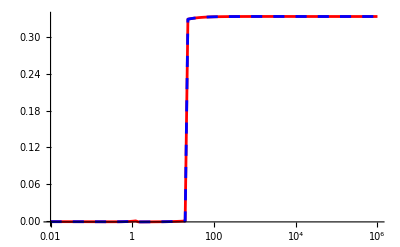

```mathematica
t0=ListLogLinearPlot[{Transpose[{f,Re[Tran[[Range[nf],1,1]]]}],
Transpose[{f,Re[Tran1[[Range[nf],1,1]]]}]},
PlotStyle->{plstyle1,plstyle3},Joined->True,PlotRange->All]
```

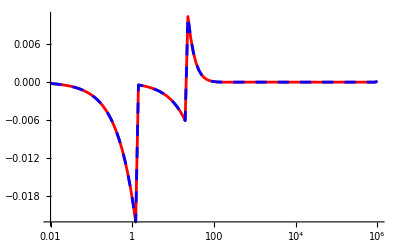

```mathematica
t1=ListLogLinearPlot[{Transpose[{f,Im[Tran[[Range[nf],1,1]]]}],
Transpose[{f,Im[Tran1[[Range[nf],1,1]]]}]},
PlotStyle->{plstyle1,plstyle3},Joined->True,PlotRange->All]
```

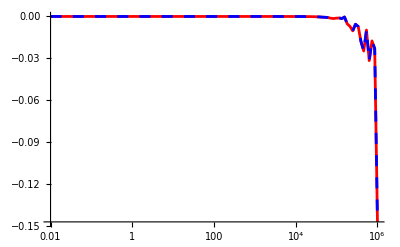

```mathematica
am0=ListLogLinearPlot[{
Transpose[{f,Re[λm[[Range[nf],1,1]]]}],
Transpose[{f,Re[λm1[[Range[nf],1,1]]]}]},
PlotStyle->{plstyle1,plstyle3},Joined->True,PlotRange->All]
```

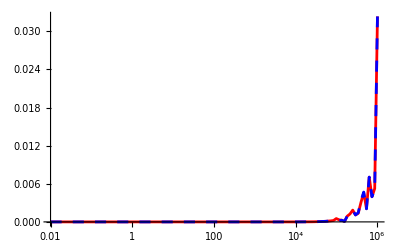

```mathematica
am1=ListLogLinearPlot[{
Transpose[{f,Im[λm[[Range[nf],1,1]]]}],
Transpose[{f,Im[λm1[[Range[nf],1,1]]]}]},
PlotStyle->{plstyle1,plstyle3},Joined->True,PlotRange->All]
```

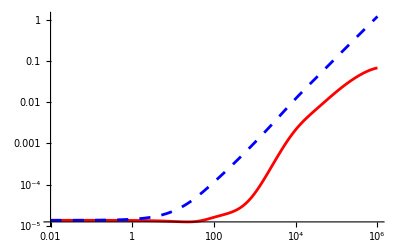

```mathematica
zp0=ListLogLogPlot[{
Transpose[{f,Re[Zss[[Range[nf],1,1]]]}],
Transpose[{f,Re[Zcs[[Range[nf],1,1]]]}]},
PlotStyle->{plstyle1,plstyle3},Joined->True,PlotRange->All]
```

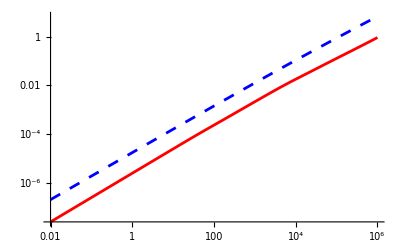

```mathematica
zp1=ListLogLogPlot[{
Transpose[{f,Im[Zss[[Range[nf],1,1]]]}],
Transpose[{f,Im[Zcs[[Range[nf],1,1]]]}]},
PlotStyle->{plstyle1,plstyle3},Joined->True,PlotRange->All]
```